# CEE-290: Models & Data HOMEWORK 5: BAYESIAN ANALYSIS A Mathematica & MATLAB Implementation Baoxiang Pan ID: 63324929

## 1.MCMC Simulation

1.Random Walk Metropolis

```mathematica
RandomWalkMetropolis[pdf_,start_,times_,proposal_]:=
Module[{f},
	f[current_]:=Module[{w,new},
		new=current+RandomVariate[proposal];
		w=Min[1,pdf[new]/pdf[current]];
		If[RandomReal[]<w,new,current]];
	Return[NestList[f,start,times]];
]
```

## II.Test Problem: N(0,1)

2.

N(0,1) is maximized when x=0.

3.

```mathematica
InverseCDF[NormalDistribution[0,1],0.025]
```

-1.95996

```mathematica
InverseCDF[NormalDistribution[0,1],0.975]
```

1.95996

The 95% uncertainty ranges of x is [-1.95996, 1.95996]

4.

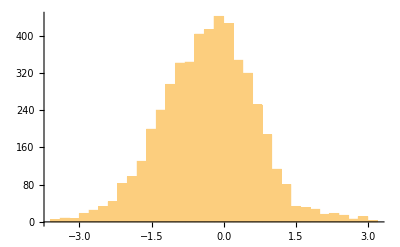

```mathematica
pdf[x_]:=PDF[NormalDistribution[0,1],x];
z=RandomWalkMetropolis[pdf,RandomReal[{-5,5}],10000,UniformDistribution[{-0.5,0.5}]];
Histogram[z[[5001;;10000]]]
```

5.

```mathematica
Mean[z[[5001;;10000]]]
```

-0.320805

```mathematica
Sqrt[Variance[z[[5001;;10000]]]]
```

0.966717

6.

6.1,Parametric Method:
Using the samples to fit normal distribution and calculate 95% range with the estimated p.d.f.
Moment Estimation:

```mathematica
μ=Mean[z[[5001;;10000]]];
σ=Sqrt[Variance[z[[5001;;10000]]]*5000/4999];
range={InverseCDF[NormalDistribution[μ,σ],0.025],InverseCDF[NormalDistribution[μ,σ],0.025]}
```

{-2.21573,-2.21573}

Maximum Likelihood Estimation

```mathematica
loglikelihood[mu_,sigma_]:=Plus@@Map[Log[PDF[NormalDistribution[mu,sigma],#]]&,z[[5001;;10000]]];
{μ,σ}=FindArgMax[loglikelihood[x,y],{{x,0.1},{y,0.9}}];
range={InverseCDF[NormalDistribution[μ,σ],0.025],InverseCDF[NormalDistribution[μ,σ],0.025]}
```

{-2.21535,-2.21535}

6.2, Non-parametric Method:
Sort the samples to find the 2.5% and 97.5% quantile.

```mathematica
zsort=Sort[z[[5001;;10000]]];
range={zsort[[Floor[0.025*Length[zsort]]]],zsort[[Floor[0.975*Length[zsort]]]]}
```

{-2.25975,1.59383}

7.

The 2.5% quantile is -2.12406; the 97.5% quantile is 1.83477.

8.

Burn in.

9.

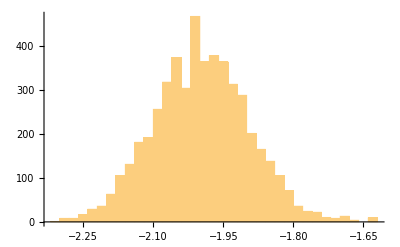

```mathematica
pdf[x_]:=PDF[NormalDistribution[-2,0.1],x];
z2=RandomWalkMetropolis[pdf,RandomReal[{-5,5}],10000,UniformDistribution[{-0.5,0.5}]];
Histogram[z2[[5001;;10000]]]
```

10.

```mathematica
Mean[z2[[5001;;10000]]]
```

-1.99734

```mathematica
Sqrt[Variance[z2[[5001;;10000]]]]
```

0.101684

11.

```mathematica
InverseCDF[NormalDistribution[-2,0.1],0.025]
```

-2.196

```mathematica
InverseCDF[NormalDistribution[-2,0.1],0.975]
```

-1.804

The 95% uncertainty ranges of x is [-2.196, 1.804].

12.

12.1,q=U[-5,5]

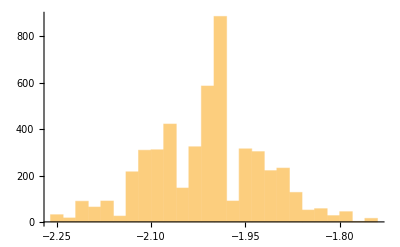

```mathematica
pdf[x_]:=PDF[NormalDistribution[-2,0.1],x];
z=RandomWalkMetropolis[pdf,RandomReal[{-5,5}],10000,UniformDistribution[{-5,5}]];
Histogram[z[[5001;;10000]]]
```

12.2,q=N[0,0.5]

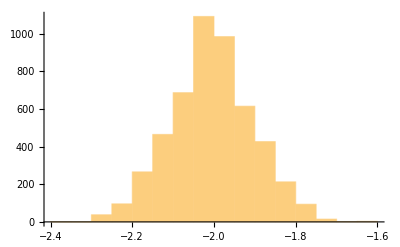

```mathematica
pdf[x_]:=PDF[NormalDistribution[-2,0.1],x];
z=RandomWalkMetropolis[pdf,RandomReal[{-5,5}],10000,NormalDistribution[0,0.5]];
Histogram[z[[5001;;10000]]]
```

13.

## III.Test Problem: Bimodal Normal Distribution

14.

14.1,Numerical Result:

```mathematica
pdf[x_]:=1/3*PDF[NormalDistribution[-5,1],x]+2/3*PDF[NormalDistribution[5,1],x];
FindMaximum[pdf[x],{x,4,98},AccuracyGoal->10,PrecisionGoal->10]
```

{0.265962,{x→5.}}

p(x|μ1,σ1,μ2,σ2)is maximized at x=5, the p.d.f. is 0.265962.

14.2,Analytical Result:
The maximum point of  probability distribution function takes place at the point that the decreasing gradient of the first component of the p.d.f. offsets the increasing gradient of the second component of the p.d.f., thus:

15.

```mathematica
mean=Integrate[pdf[x]*x,{x,-Infinity,Infinity}]
```

5/3

```mathematica
variance=Integrate[pdf[x]*(x-mean)^2,{x,-Infinity,Infinity}]
```

209/9

16.

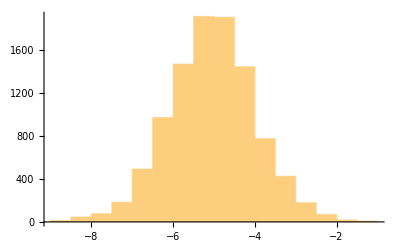

```mathematica
z=RandomWalkMetropolis[pdf,RandomReal[{-10,10}],25000,UniformDistribution[{-0.5,0.5}]];
Histogram[z[[15001;;25000]]]
```

17.

```mathematica
Mean[z[[5001;;10000]]]
```

-4.81896

```mathematica
Sqrt[Variance[z[[5001;;10000]]]]
```

1.09639

18.

No.

19(1).

Yes.

## IV.Multiple Chain Methods: DE-MC and DREAM

Original Differential Evolutionary Algorithm

```mathematica
DifferentialEvolution[range_,FitnessFunction_,times_]:=
Module[{population,Evolution,size=1000,CR=0.8,F=1,final},
	population=Table[Module[{point},
						point=Map[#[[1]]+RandomReal[#[[2]]-#[[1]]]&,range];
						{FitnessFunction[point],point}],
				{i,size}];
	Evolution[population_]:=
		Module[{CandidateGeneration},
			CandidateGeneration[point_]:=
				Module[{ConstructGeneration,vpoint,upoint,rupoint},
					ConstructGeneration[]:=Module[{potentialpoints},
											potentialpoints=RandomSample[population,3];
											Return[If[MemberQ[potentialpoints,point],ConstructGeneration[],potentialpoints]]];
					vpoint[]:=Module[{points},
						points=ConstructGeneration[];
						Return[points[[1]]+F*(points[[2]]-points[[3]])]];
					upoint[]:=Module[{vpoints,points},
						vpoints=vpoint[];
						points=Table[If[RandomReal[]<CR,vpoints[[2,i]],point[[2,i]]],{i,Length[point]}];
						Return[{FitnessFunction[points],points}]];
					rupoint=upoint[];
				Return[If[rupoint[[1]]>point[[1]],point,rupoint]]];									
			Return[Map[CandidateGeneration,population]]];
	Return[SortBy[Nest[Evolution,population,times],First][[1]]]];
```

19(2). Differential Evolutionary Markov Chain Monte Carlo Algorithm

```mathematica
temperature=1;
DEMC[range_,times_,pdf_]:=
Module[{population,Evolution,size=10,F,final,b=0.000001},
	F=2.4/Sqrt[2*Length[range]];
	population=Table[Map[#[[1]]+RandomReal[#[[2]]-#[[1]]]&,range],{i,size}];
	Evolution[population_]:=
		Module[{CandidateGeneration},
			CandidateGeneration[point_]:=
				Module[{ConstructGeneration,vpoint,selection},
					ConstructGeneration[]:=Module[{potentialpoints},
											potentialpoints=RandomSample[population,2];
											Return[If[MemberQ[potentialpoints,point],ConstructGeneration[],potentialpoints]]];
					vpoint[]:=Module[{points},
						points=ConstructGeneration[];
						Return[point+F*(points[[1]]-points[[2]])+RandomReal[{-b,b},Length[point]]]];
					selection[]:=Module[{upoint},
						upoint=vpoint[];
						Return[If[Log[pdf[upoint]/pdf[point]]>temperature*Log[RandomReal[]],
									upoint,
									point]]];
					Return[selection[]]];					 
			Return[Map[CandidateGeneration,population]]];
	Return[NestList[Evolution,population,times]]];
```

20.

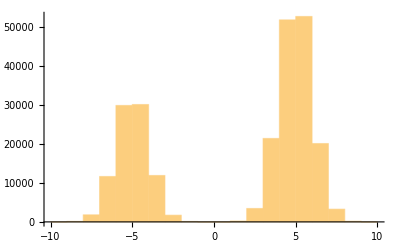

```mathematica
pdf[x_]:=1/3*PDF[NormalDistribution[-5,1],x[[1]]]+2/3*PDF[NormalDistribution[5,1],x[[1]]];
r=DEMC[{{-5,5}},25000,pdf];
track=Table[Map[#[[i,1]]&,r],{i,Length[r[[1]]]}];
mtrack=Flatten[r];
Histogram[Drop[mtrack,10000]]
```

```mathematica
ListPlot[track,PlotLegends->SwatchLegend[{"Track 1","Track 2","Track 3","Track 4","Track 5"},LegendMarkerSize-> 10],AxesLabel->{"Sample Number","Value"}]
```

-Graphics-

21.

The relation between mean value of each track and sample numbers is drawn as follow:

```mathematica
p1=ListPlot[{{25001,1.67}},PlotStyle->PointSize[0.03]];
pmean=ListPlot[Table[Table[Mean[track[[i]][[1;;j]]],{j,Length[track[[i]]]}],{i,Length[track]}],PlotLegends->SwatchLegend[{"Track 1","Track 2","Track 3","Track 4","Track 5","Track 6","Track 7","Track 8","Track 9","Track 10"},LegendMarkerSize-> 10]];
Show[p1,pmean,PlotRange->Automatic,AxesLabel->{"Sample Number","Mean"}]
```

-Graphics-

The relation between variance of each track and sample numbers is drawn as follow:

```mathematica
p2=ListPlot[{{25001,209/9.0}},PlotStyle->PointSize[0.03],PlotRange->All];
pvariance=ListPlot[Table[Table[Variance[track[[i]][[1;;j]]],{j,2,Length[track[[i]]]}],{i,Length[track]}],PlotLegends->SwatchLegend[{"Track 1","Track 2","Track 3","Track 4","Track 5","Track 6","Track 7","Track 8","Track 9","Track 10"},LegendMarkerSize-> 10]];
Show[p2,pvariance,PlotRange->Automatic,AxesLabel->{"Sample Number","Variance"}]
```

-Graphics-

22.

More accurate estimation of p.d.f.

## V.Real-world Study - Hydrologic Modelling

23.

The reason is to avoid numerical overflow.

24.

α(x_(t+1),z|Ỹ)=min((p(z|Ỹ))/(p(x_(t-1)|Ỹ)),1)
		  =min(e^(log(p(z|Ỹ)))/e^(log(p(x_(t-1)|Ỹ))),1)
		  =min(exp[logp(z|Ỹ)-logp(x_(t-1|Ỹ))],1)

25.

Since the HModel uses API between MATLAB code and C code, the DE-MC algorithm is re-implemented in MATLAB using an imperative manner to adapt to the former code. 
The MATLAB implementation of DE-MC is as follows:

26.

1,Using the Mean value.

2,Using  arg(max( p.d.f)).

27.

Parameter | Symbol | Mean | Std | Units
Maximum interception | I_max | □ | □ | mm
Soil water storage capacity | S_max | □ | □ | mm
Maximum percolation rate | Q_max | □ | □ | mm/d
Evaporation parameter | α_E | □ | □ | -
Runoff parameter | α_F | □ | □ | -
Time constant,fast reservoir | K_F | □ | □ | days
Time constant,slow reservoir | K_S | □ | □ | days